(1-x) y[0]+x y[1]

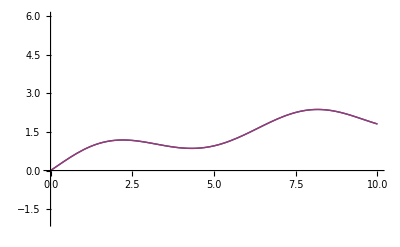

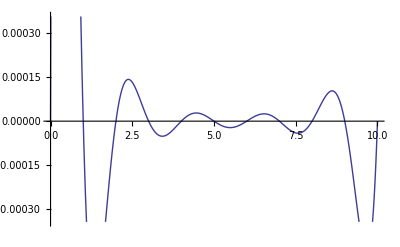

```mathematica
ClearAll[y,Y,a,b,n,f,x,A]
Unprotect[Power];
0^0=1;
Protect[Power];
a=0;b=10;
n=10; (*Anzahl Integrationsstellen*)
k=10;(*Anzahl Stützstellen*)
f[x_]:=(Exp[x/10] Sin[x]+x)/Log[x^2+10]
x[k_]:=a+(k (b-a))/n
A[n_]:=Table[(∏_(k=0)^n (x-x[k])^If[k≠m,1,0])/(∏_(k=0)^n (x[m]-x[k])^If[k≠m,1,0]),{m,0,n}]
Y[n_]:=Table[y[k],{k,0,n}]
A[1].Y[1]
y[k_]:=f[x[k]]
Plot[{f[z],A[k].Y[k]//.x->z},{z,0,10},PlotRange->{-2,6}]
Plot[f[z]-A[k].Y[k]//.x->z,{z,0,10}]
```

```mathematica
ClearAll[y,x]
A[3].Y[3]
```

((x-x[1]) (x-x[2]) (x-x[3]) y[0])/((x[0]-x[1]) (x[0]-x[2]) (x[0]-x[3]))+((x-x[0]) (x-x[2]) (x-x[3]) y[1])/((-x[0]+x[1]) (x[1]-x[2]) (x[1]-x[3]))+((x-x[0]) (x-x[1]) (x-x[3]) y[2])/((-x[0]+x[2]) (-x[1]+x[2]) (x[2]-x[3]))+((x-x[0]) (x-x[1]) (x-x[2]) y[3])/((-x[0]+x[3]) (-x[1]+x[3]) (-x[2]+x[3]))

Wie integriere ich eine Nullstellenform darstellung eines Polynoms? Partielle Integration k mal.

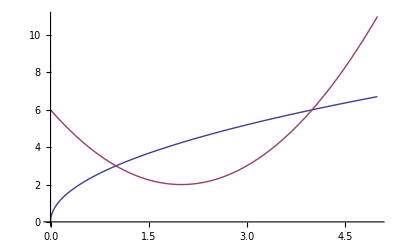

```mathematica
Plot[{3Sqrt[x],x^2-4x+6},{x,0,5}]
```

```mathematica
Integrate[3Sqrt[x]-(x^2-4x+6),{x,1,4}]
```

5